```mathematica
NotebookEvaluate[NotebookDirectory[]<>"NOMexplicitPhaseFieldMain.nb"];
```

```mathematica
(*Create the model*)
xmin={0.,0.};xmax=10^-3{1.,1.};{width,height}=xmax-xmin;dx=10^-3 0.005;
coord=GridDomain[xmin,xmax,dx];
vol=ConstantArray[dx^2,Length[coord]];
Nnode=Length[coord];ndim=Length[coord[[1]]];
ndof=ndim Nnode;
Es=210. 10^9;mu=0.3;rho=7800.;pmass=rho vol;etype=2;
Gc=2700.;pfModulus=4.;pfModulusT=1.;(*phase field length scale.*)
{bulkK,shearG}=PlaneStress[Es,mu,True];
penCoef=1.;
numNei=8;
NeiList=Nearest[coord->Automatic,coord,numNei+1];
WeiF[r_]:=1./r^2;
coord0=coord;mesh1=MyDelaunayMesh[coord0];(*mesh for postprocess only*)
acc=ConstantArray[0.,{Nnode,ndim}];
accNew=acc;
internalF=acc;
velo=acc;
veloSound=Sqrt[Es/rho];tIncMax=dx/veloSound;
ctime=0.;
tInc=0.8tIncMax;
TotalTime=10 tInc;
pfList=ConstantArray[0.,Nnode];
gradS=ConstantArray[0.,{Nnode,ndim}];lapS=pfList;
enerP=pfList;
uvw=0.;
deformList=0.;
```

```mathematica
neicoord0=NeighborPartition[coord0,NeiList];
neivol=NeighborPartition[vol,NeiList];
WeiF[r_]:=1./r^2;
neiWeiL=WeightByNeighbor[neicoord0,WeiF];
{trKList,invKList}=KmatrixL[neicoord0,neiWeiL,neivol];
```

```mathematica
nfix=FindPoints[coord,xmin-{0.5 dx,0.5 dx},xmin+{height+0.5 dx,0.5dx}];
nvelo=FindPoints[coord,xmax-{height+0.5 dx,0.5dx},xmax+{0.5 dx,0.5 dx}];
dofFix=ConstantArray[{0.,0.},Length[nfix]];(*dof in y direction*)
forceY={0.,1.};
veloValue=ConstantArray[forceY,Length[nvelo]];
nforce={};
dofForce={};
xmid=0.5 (xmin+xmax);
npf=FindPoints[coord,xmid-{0.5 width,1dx},xmid+{0.,0.6 dx}];
```

```mathematica
KineticEnergy={};
timeList={};
strainEnergy={};
pfEnergy={};
uMaxList={};
vMaxList={};
reactionForceList={};
jstep=1;
```

```mathematica
$HistoryLength=1;
```

```mathematica
statisticInterval=5;outputInterval=60;printInterval=30;ls=1.25dx;
numstep=9000;

resiMaxList={};

fpath=CreateFolder[ToString[Gc]<>"tensionV1ls1.25dxTreshold"<>ToString[IntegerPart[width/dx]]];gcl=0.Gc/ls;L2pfresidu=0.;L2pfInc=0.;pfInc=0.;tolL2pfInc=10.^-4;
tolpfIncMax=10.^-3;
resiMaxTol=10.^-2;subInterMax=20;
```

```mathematica
Do[coord+=tInc velo+(0.5 tInc^2)acc;
coord[[nfix]]=coord0[[nfix]]+dofFix;(*displacement constraint*)
velo[[nfix]]=0.;
uvw=coord-coord0;
neicoord=NeighborPartition[coord,NeiList];
neipfList=NeighborPartition[pfList,NeiList];
{gradS,deformList}=FSmatrixL[neipfList,neicoord,neicoord0,neivol,invKList,neiWeiL];
{enerP,enerN,stress,stressP}=StressList[ndim,bulkK,shearG,gcl,deformList];kMax=1;resiMax1=0.;
resiMax2=0.;
Do[
lapS=LaplaceSListAll[NeiList,neicoord0,gradS,neipfList,invKList,trKList,neivol,penCoef,neiWeiL];
lapS/=vol;
pfresi=PhaseFieldResidual[ls,Gc,lapS,pfList,enerP];
If[k==1,resiMax1=Max[pfresi]];
resiMax2=Max[pfresi];
AppendTo[resiMaxList,resiMax2];
L2pfInc=Sqrt[(pfresi vol).pfresi/Total[vol]];
If[k==1,pfModulusT=Max[pfModulus,20 resiMax1]];
pfList+=1./pfModulusT*pfresi;

pfList[[npf]]=1.;kMax=k;
If[k==1 && resiMax1<resiMaxTol,Break[]];
If[resiMax2<tolpfIncMax || k==subInterMax,Break[],neipfList=NeighborPartition[pfList,NeiList];gradS=GradSmatrixL[neipfList,neicoord0,neivol,invKList,neiWeiL]];
,{k,1,subInterMax}];
(*Print["subIteration:",kMax," resiMax:",resiMax2," resiMax0:",resiMax1];*)
stress+=((1.-pfList)^2-1.)stressP;
internalF=ForceListAllpf[NeiList,neicoord,neicoord0,stress,deformList,invKList,trKList,neivol,penCoef shearG,neiWeiL,pfList];
internalF[[nforce]]+=dofForce;(*add boundary forces to the internal force vector*) 
accNew=internalF/pmass;
velo+=0.5 tInc (acc+accNew);
velo[[nvelo]]=veloValue;(*velocity constraint*)
accNew[[nvelo]]=0.;
accNew[[nfix]]=0.;
acc=accNew;

ctime+=tInc;jstep++;
If[Mod[jstep,statisticInterval]==1,AppendTo[timeList,ctime];AppendTo[KineticEnergy,0.5 pmass .Table[velo[[i]].velo[[i]],{i,Length[velo]}]];AppendTo[strainEnergy,StrainEnergyCal[enerP,enerN,vol,pfList]];AppendTo[pfEnergy,Gc (PhaseFieldEnergy[pfList,gradS,ls,vol])];
AppendTo[reactionForceList,Total[internalF[[nfix]]]]];
If[Mod[jstep,printInterval]==1,Print["acc max:",Max[accNew],",vel max:",Max[velo],",umax: ",Max[uvw]];
Print["step=",jstep,",t=",ctime," done"];Print[Plot2DField[uvw[[All,2]],mesh1]];Print[Plot2DField[velo[[All,1]],mesh1]];Print[Plot2DField[pfList,mesh1]]];
If[Mod[jstep,outputInterval]==1,OvitoOutput[fpath,"res",jstep,"x y ux uy pf vx vy",coord0,coord-coord0,pfList,velo];];
(*Print[Plot2DField[pfList,mesh1]]*)
,{i,numstep}];
Plot2DField[pfList,mesh1]
ListPlot[Log10[resiMaxList[[2;;]]],PlotRange->All]
```

```mathematica
SaveToCell[{timeList,resiMaxList,KineticEnergy,strainEnergy,pfEnergy,reactionForceList},"ls=1.25dx,200,1G"]
```

```mathematica
{timeList1,resiMaxList1,KineticEnergy1,strainEnergy1,pfEnergy1,reactionForceList1}="ls=1.25dx,200,1G";
```

```mathematica
{timeList2,resiMaxList2,KineticEnergy2,strainEnergy2,pfEnergy2}="ls=1.25dx,100";
```

displacement -load curve from Miehe paper

```mathematica
ufRef={{0.000008673693456301987,1.4492753623186445},{0.0001474371039588431,23.18840579710138},{0.0003034851621808144,42.028985507246375},{0.0004942593638245813,69.56521739130426},{0.0007023495827843654,97.10144927536226},{0.0009191291799987452,127.53623188405788},{0.0011012140033879161,152.17391304347825},{0.0012919725202333902,178.26086956521726},{0.0014653993349645524,202.89855072463763},{0.0016648158604680348,228.98550724637676},{0.0018642480707698097,256.52173913043475},{0.0020636489114749983,281.159420289855},{0.00224573373486417,305.7971014492754},{0.0024451345755693585,330.4347826086955},{0.0026358774076165386,355.0724637681159},{0.0028266045548654235,378.2608695652174},{0.0030433370976849236,404.3478260869565},{0.003251395947048121,428.9855072463767},{0.0034941182006399405,456.52173913043475},{0.003693487671748541,478.2608695652174},{0.003901530836313445,501.4492753623188},{0.004144206035510383,524.6376811594203},{0.004360891523935003,546.3768115942029},{0.004594893029675639,568.1159420289855},{0.004863542254846603,591.304347826087},{0.0051408338038772825,613.0434782608695},{0.0053487828596524255,627.536231884058},{0.0055393688437166706,637.6811594202898},{0.005669254658385094,639.1304347826086},{0.005721030177551917,623.1884057971014},{0.005755270092226615,586.9565217391304},{0.005797964113181504,531.8840579710145},{0.005849316142794404,476.8115942028985},{0.0059092007026789635,410.1449275362318},{0.005960427253905515,343.47826086956513},{0.006003058535667231,282.6086956521739},{0.0060543478260869565,221.7391304347825},{0.006088289729594078,157.9710144927535},{0.006096257607127173,94.20289855072451},{0.006104554865424431,60.86956521739114}};
```

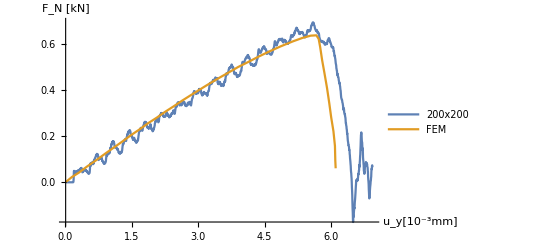

```mathematica
axesLabel={"u_y[10^-3mm]","F_N [kN]"};
PlotXYL[timeList1 1000000,reactionForceList1[[All,2]]/1000000,"200x200",ufRef[[All,1]] 1000,ufRef[[All,2]]/1000,"FEM"]
```

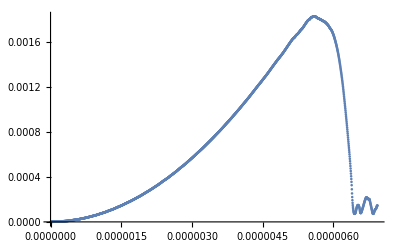

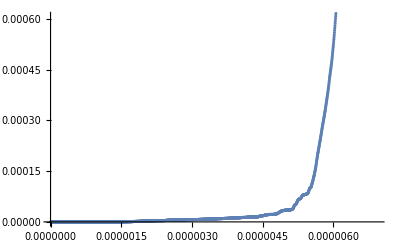

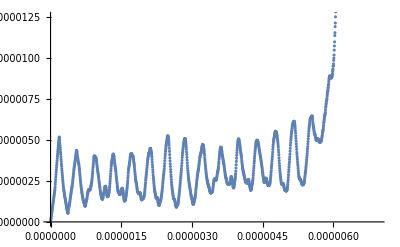

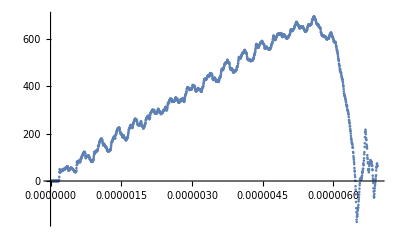

```mathematica
ListPlot[{timeList,strainEnergy/1000}ᵀ]
ListPlot[{timeList,(pfEnergy-pfEnergy[[3]])/1000}ᵀ]
ListPlot[{timeList,KineticEnergy/1000}ᵀ]
ListPlot[{timeList,reactionForceList[[All,2]]/1000}ᵀ]
```

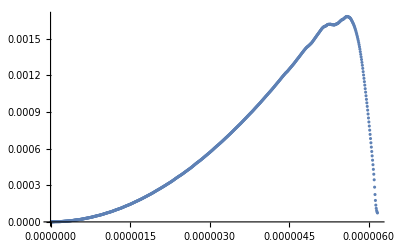

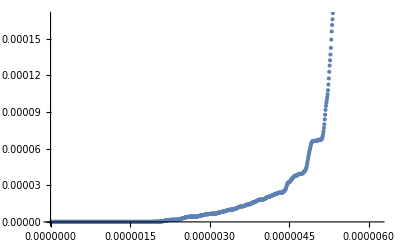

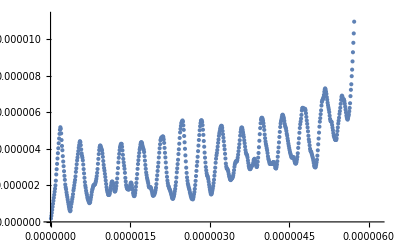

```mathematica
1.25dx,1G
```

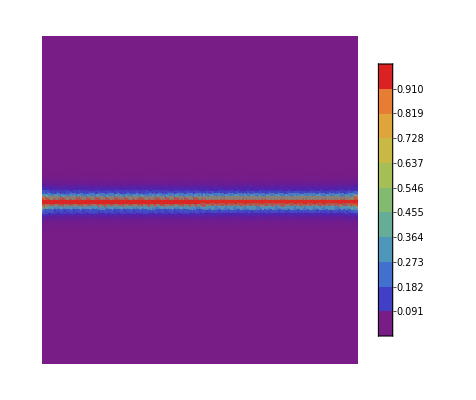

```mathematica
Plot2DField[uvw[[All,2]],mesh1]
Plot2DField[velo[[All,2]],mesh1]
Plot2DField[pfList,mesh1](*1.25dx*)
```